```mathematica
a=10;
i = 0;
M1 = 5;
M2 = 10;
R1 = 19;
R2 =10;
T1 = 8000;
T2= 13000;
ec = 0.0;
x1 = -50;
x2 = 0;
y1 = 0;
y2 = 0;
z1 = 0;
z2 =0;
size=70;
xc = x1 +( x2-x1)*M2/(M1+M2);
yc =y1+(y2-y1)*M2/(M1+M2);
zc=0;
(*w =ContourPlot3D[{M1/(((x1-x)^2+(y1-y)^2+(z1-z)^2)^0.5)+M2/(((x2-x)^2+(y2-y)^2+(z2-z)^2)^0.5)+(M1+M2)/(x2-x1)^3*√((xc-x)^2+(yc-y)^2)==3.638}, {x, -size, size}, {y, -size, size},{z, -size,size},ColorFunction->Blue, ImageSize->2000,PlotPoints->20, Mesh->None, ViewPoint->{1000,0,0}, Boxed->False, Axes->False, (*Lighting->{{"Ambient",White}},*) ContourStyle->Blue,PlotRange->{{-size, size},{-size,size},{-size,size}},SphericalRegion->True,ViewCenter->{0.5(1+xc/size),0.5,0.5}]*)
```

```mathematica
(*Lighting->{{"Ambient",White}}*)
plot[ax_,by_,cz_]=Evaluate[ContourPlot3D[{M1/(((x1-x)^2+(y1-y)^2+(z1-z)^2)^0.5)+M2/(((x2-x)^2+(y2-y)^2+(z2-z)^2)^0.5)+(M1+M2)/(x2-x1)^3*√((xc-x)^2+(yc-y)^2)==3.637}, {x, -size, size}, {y, -size, size},{z, -size,size},Lighting->{{"Ambient", White}}, ImageSize->800,PlotPoints->20, Mesh->None, ViewPoint->{1000,0,0}, Boxed->False,ContourStyle->Directive[Blue],Axes->False,PlotRange->{{-size, size},{-size,size},{-size,size}},SphericalRegion->True]]/.{1000,0,0}->{ax,by,cz};
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

```mathematica
plot[1000*Sin[Pi]+xc,1000*Cos[Pi],500]
```

-Graphics3D-

```mathematica
number = 100;
curva=Table[{i/(2Pi),Length@PixelValuePositions[ plot[1000*Sin[i]+xc, 1000*Cos[i],0],Blue,0.1]}, {i, 0, 2Pi, 2Pi/number}];
```

```mathematica
(*Animate[{plot[1000*Sin[tt], 1000*Cos[tt], 0],Show[ListPlot[curva,ImageSize->500],Graphics[Line[{{tt,0},{tt,1.2}}]]]},{tt,0,2Pi}]*)
```

```mathematica
curva=Table[{N[curva[[i,1]],6],N[curva[[i,2]]/23330,6]},{i,1,number}]
```

{{0,0.999914},{0.01,0.9991},{0.02,0.997257},{0.03,0.994514},{0.04,0.990099},{0.05,0.984784},{0.06,0.978826},{0.07,0.971453},{0.08,0.962795},{0.09,0.954393},{0.1,0.944363},{0.11,0.933948},{0.12,0.920489},{0.13,0.903986},{0.14,0.883412},{0.15,0.859837},{0.16,0.830947},{0.17,0.7994},{0.18,0.763652},{0.19,0.724561},{0.2,0.682683},{0.21,0.638448},{0.22,0.591599},{0.23,0.54342},{0.24,0.494642},{0.25,0.445306},{0.26,0.494213},{0.27,0.543678},{0.28,0.591599},{0.29,0.638148},{0.3,0.682726},{0.31,0.724732},{0.32,0.763609},{0.33,0.799271},{0.34,0.831762},{0.35,0.859151},{0.36,0.883841},{0.37,0.903858},{0.38,0.920489},{0.39,0.933819},{0.4,0.944792},{0.41,0.954136},{0.42,0.962752},{0.43,0.971239},{0.44,0.978483},{0.45,0.985169},{0.46,0.990056},{0.47,0.994599},{0.48,0.997685},{0.49,0.999529},{0.5,1.},{0.51,0.999271},{0.52,0.997557},{0.53,0.994299},{0.54,0.989756},{0.55,0.984612},{0.56,0.977968},{0.57,0.970081},{0.58,0.962109},{0.59,0.953536},{0.6,0.943892},{0.61,0.932748},{0.62,0.918988},{0.63,0.902658},{0.64,0.882169},{0.65,0.857865},{0.66,0.829533},{0.67,0.797428},{0.68,0.762195},{0.69,0.723318},{0.7,0.681312},{0.71,0.637077},{0.72,0.590699},{0.73,0.543249},{0.74,0.494171},{0.75,0.445435},{0.76,0.494514},{0.77,0.542778},{0.78,0.590656},{0.79,0.637034},{0.8,0.681226},{0.81,0.722932},{0.82,0.76168},{0.83,0.797428},{0.84,0.829361},{0.85,0.857608},{0.86,0.882169},{0.87,0.902529},{0.88,0.919546},{0.89,0.932919},{0.9,0.944063},{0.91,0.953579},{0.92,0.962195},{0.93,0.970553},{0.94,0.977925},{0.95,0.984398},{0.96,0.989413},{0.97,0.994299},{0.98,0.997214},{0.99,0.9988}}

```mathematica
curvaa=Table[{N[curva[[i,1]],6],N[-2.5 Log10[curva[[i,2]]],6]},{i,1,number}]
```

{{0,0.0000930804},{0.01,0.000977742},{0.02,0.00298254},{0.03,0.00597329},{0.04,0.0108039},{0.05,0.016648},{0.06,0.0232368},{0.07,0.0314454},{0.08,0.0411658},{0.09,0.0506813},{0.1,0.062152},{0.11,0.0741936},{0.12,0.0899539},{0.13,0.109595},{0.14,0.134592},{0.15,0.16396},{0.16,0.201066},{0.17,0.24309},{0.18,0.292761},{0.19,0.349813},{0.2,0.414452},{0.21,0.487186},{0.22,0.569932},{0.23,0.66216},{0.24,0.764272},{0.25,0.878352},{0.26,0.765214},{0.27,0.661646},{0.28,0.569932},{0.29,0.487696},{0.3,0.414384},{0.31,0.349556},{0.32,0.292822},{0.33,0.243264},{0.34,0.200003},{0.35,0.164826},{0.36,0.134065},{0.37,0.10975},{0.38,0.0899539},{0.39,0.0743431},{0.4,0.0616594},{0.41,0.0509739},{0.42,0.0412141},{0.43,0.031685},{0.44,0.0236172},{0.45,0.0162228},{0.46,0.0108509},{0.47,0.0058797},{0.48,0.00251598},{0.49,0.000512041},{0.5,0.},{0.51,0.000791438},{0.52,0.00265592},{0.53,0.00620729},{0.54,0.01118},{0.55,0.0168371},{0.56,0.0241881},{0.57,0.0329795},{0.58,0.0419395},{0.59,0.051657},{0.6,0.0626943},{0.61,0.0755897},{0.62,0.0917249},{0.63,0.111192},{0.64,0.136121},{0.65,0.166452},{0.66,0.202916},{0.67,0.245771},{0.68,0.294835},{0.69,0.351677},{0.7,0.416636},{0.71,0.489521},{0.72,0.571585},{0.73,0.662503},{0.74,0.765308},{0.75,0.878039},{0.76,0.764555},{0.77,0.663445},{0.78,0.571664},{0.79,0.489594},{0.8,0.416772},{0.81,0.352257},{0.82,0.295568},{0.83,0.245771},{0.84,0.203141},{0.85,0.166778},{0.86,0.136121},{0.87,0.111347},{0.88,0.0910668},{0.89,0.0753902},{0.9,0.0624971},{0.91,0.0516082},{0.92,0.0418427},{0.93,0.0324519},{0.94,0.0242357},{0.95,0.0170734},{0.96,0.0115562},{0.97,0.00620729},{0.98,0.0030292},{0.99,0.00130385}}

```mathematica
TableForm[Round[curvaa,0.000001]]
```

0. | 0.000093
0.01 | 0.000978
0.02 | 0.002983
0.03 | 0.005973
0.04 | 0.010804
0.05 | 0.016648
0.06 | 0.023237
0.07 | 0.031445
0.08 | 0.041166
0.09 | 0.050681
0.1 | 0.062152
0.11 | 0.074194
0.12 | 0.089954
0.13 | 0.109595
0.14 | 0.134592
0.15 | 0.16396
0.16 | 0.201066
0.17 | 0.24309
0.18 | 0.292761
0.19 | 0.349813
0.2 | 0.414452
0.21 | 0.487186
0.22 | 0.569932
0.23 | 0.66216
0.24 | 0.764272
0.25 | 0.878352
0.26 | 0.765214
0.27 | 0.661646
0.28 | 0.569932
0.29 | 0.487696
0.3 | 0.414384
0.31 | 0.349556
0.32 | 0.292822
0.33 | 0.243264
0.34 | 0.200003
0.35 | 0.164826
0.36 | 0.134065
0.37 | 0.10975
0.38 | 0.089954
0.39 | 0.074343
0.4 | 0.061659
0.41 | 0.050974
0.42 | 0.041214
0.43 | 0.031685
0.44 | 0.023617
0.45 | 0.016223
0.46 | 0.010851
0.47 | 0.00588
0.48 | 0.002516
0.49 | 0.000512
0.5 | 0.
0.51 | 0.000791
0.52 | 0.002656
0.53 | 0.006207
0.54 | 0.01118
0.55 | 0.016837
0.56 | 0.024188
0.57 | 0.03298
0.58 | 0.041939
0.59 | 0.051657
0.6 | 0.062694
0.61 | 0.07559
0.62 | 0.091725
0.63 | 0.111192
0.64 | 0.136121
0.65 | 0.166452
0.66 | 0.202916
0.67 | 0.245771
0.68 | 0.294835
0.69 | 0.351677
0.7 | 0.416636
0.71 | 0.489521
0.72 | 0.571585
0.73 | 0.662503
0.74 | 0.765308
0.75 | 0.878039
0.76 | 0.764555
0.77 | 0.663445
0.78 | 0.571664
0.79 | 0.489594
0.8 | 0.416772
0.81 | 0.352257
0.82 | 0.295568
0.83 | 0.245771
0.84 | 0.203141
0.85 | 0.166778
0.86 | 0.136121
0.87 | 0.111347
0.88 | 0.091067
0.89 | 0.07539
0.9 | 0.062497
0.91 | 0.051608
0.92 | 0.041843
0.93 | 0.032452
0.94 | 0.024236
0.95 | 0.017073
0.96 | 0.011556
0.97 | 0.006207
0.98 | 0.003029
0.99 | 0.001304

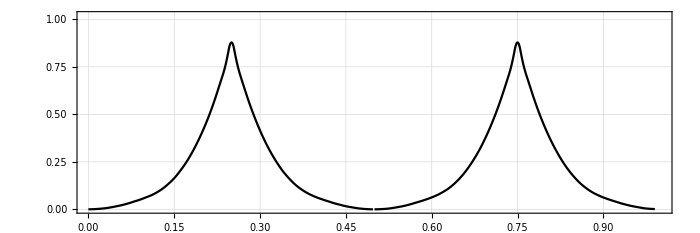

```mathematica
graphw=ListPlot[curvaa, Joined->True,InterpolationOrder->2,FrameStyle->12, PlotTheme->"Detailed",PlotStyle->RGBColor[0,0,0],FrameStyle->Directive[Black,Thickness[Medium]], AspectRatio->1/3,ImageSize->700,PlotRange->{{0,1},{0.0,1.02}}]
```

```mathematica
Export["/Users/AShepelev/Documents/Light_curve/W_UMa/UMa_curve_i300.gif",Table[Show[graphw,Graphics[{PointSize->0.02,Point[{{ii,Interpolation[curva][ii]}}]},ImageSize->500]]/.ii->i,{i,0, 1, 1/60}]]
```

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

/Users/AShepelev/Documents/Light_curve/W_UMa/UMa_curve_i300.gif

```mathematica
Export["/Users/AShepelev/Documents/Light_curve/W_UMa/W_UMa_i300.gif",Table[ImageCrop[Rasterize[plot[1000Sin[t]+xc,1000Cos[t],300]],{300,200}],{t, 0, 2Pi, Pi/30}]]
```

/Users/AShepelev/Documents/Light_curve/W_UMa/W_UMa_i300.gif

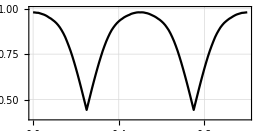

```mathematica
ListPlot[curva, Joined->True,InterpolationOrder->1, PlotTheme->"Detailed",PlotStyle->RGBColor[0,0,0], PlotRange->{{0,1},{0.4,1}},FrameStyle->Directive[Black,Thickness[Medium]], AspectRatio->1/2]
```

```mathematica
r = 30;
d =0.5;

plotblyr[ax_,by_,cz_]=Evaluate[Show[ContourPlot3D[{M1/(((x1-x)^2+(y1-y)^2+(z1-z)^2)^0.5)+M2/(((x2-x)^2+(y2-y)^2+(z2-z)^2)^0.5)+(M1+M2)/(x2-x1)^3*√((xc-x)^2+(yc-y)^2)==0.585}, {x, -size, -30}, {y, -size, size},{z, -size,size}, ImageSize->800,PlotPoints->20, Mesh->None, ViewPoint->{1000,0,0}, Boxed->False,ContourStyle->Directive[Red],Axes->False,PlotRange->{{-size, size},{-size,size},{-size,size}},SphericalRegion->True,Lighting->{{"Ambient", White}}],Graphics3D[{Blue,Sphere[{x2,y2,z2},R2]},Axes->True ], Graphics3D[{Yellow,EdgeForm[None],Cylinder[ {{x2,y2,-d}, {x2, y2, d}},r]},Axes->True, Lighting->{{"Ambient", White}}],Lighting->{{"Ambient", White}}]]/.{1000,0,0}->{ax,by,cz};
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

```mathematica
plotblyr[0,1000,300]
```

-Graphics3D-

```mathematica
-
```

```mathematica
Export["/Users/AShepelev/Desktop/__d.gif",Table[plotblyr[1000*Sin[i],1000*Cos[i],300]],{500,300}],{i, 0, 2*Pi,Pi/30}]]
```

/Users/AShepelev/Desktop/__d.gif

```mathematica
T3=5000;
curved= Parallelize[Table[{i/(2Pi),((T2/T1)^4*Length@PixelValuePositions[plotblyr[1000*Sin[i]+xc, 1000*Cos[i],200],Blue,0.1]+(T3/T1)^4*Length@PixelValuePositions[plotblyr[1000*Sin[i]+xc, 1000*Cos[i],200],Yellow,0.1]+Length@PixelValuePositions[plotblyr[1000*Sin[i]+xc, 1000*Cos[i],200],Red,0.1])}, {i, 0, 2Pi, Pi/50}]];
```

```mathematica
curvedtmp =Table[{curved[[i,1]], Round[-2.5Log10[curved[[i,2]]/23932],0.00001]},{i,1,100,1}];
```

```mathematica
TableForm[N[curvedtmp]]
```

0. | 0.00024
0.01 | 0.00055
0.02 | 0.00091
0.03 | 0.00221
0.04 | 0.0042
0.05 | 0.00642
0.06 | 0.00924
0.07 | 0.01286
0.08 | 0.01788
0.09 | 0.02381
0.1 | 0.03049
0.11 | 0.03787
0.12 | 0.0475
0.13 | 0.05622
0.14 | 0.06883
0.15 | 0.07959
0.16 | 0.09328
0.17 | 0.10719
0.18 | 0.12109
0.19 | 0.13075
0.2 | 0.13803
0.21 | 0.14671
0.22 | 0.15482
0.23 | 0.15888
0.24 | 0.16094
0.25 | 0.16059
0.26 | 0.16063
0.27 | 0.15994
0.28 | 0.15428
0.29 | 0.14728
0.3 | 0.1387
0.31 | 0.13004
0.32 | 0.12148
0.33 | 0.10786
0.34 | 0.0935
0.35 | 0.07983
0.36 | 0.06835
0.37 | 0.05619
0.38 | 0.04696
0.39 | 0.03781
0.4 | 0.02994
0.41 | 0.024
0.42 | 0.01714
0.43 | 0.01334
0.44 | 0.00937
0.45 | 0.00637
0.46 | 0.00461
0.47 | 0.00194
0.48 | 0.0003
0.49 | 0.00003
0.5 | 0.00013
0.51 | 0.00016
0.52 | 0.00076
0.53 | 0.00161
0.54 | 0.00231
0.55 | 0.00417
0.56 | 0.00735
0.57 | 0.00912
0.58 | 0.01255
0.59 | 0.0154
0.6 | 0.01793
0.61 | 0.02192
0.62 | 0.02405
0.63 | 0.02802
0.64 | 0.03019
0.65 | 0.03404
0.66 | 0.03673
0.67 | 0.03999
0.68 | 0.04374
0.69 | 0.08069
0.7 | 0.15208
0.71 | 0.24952
0.72 | 0.35499
0.73 | 0.45212
0.74 | 0.50989
0.75 | 0.52789
0.76 | 0.5101
0.77 | 0.45321
0.78 | 0.35556
0.79 | 0.24876
0.8 | 0.15236
0.81 | 0.08005
0.82 | 0.04435
0.83 | 0.03955
0.84 | 0.03628
0.85 | 0.0334
0.86 | 0.03025
0.87 | 0.02726
0.88 | 0.0245
0.89 | 0.02223
0.9 | 0.01713
0.91 | 0.01533
0.92 | 0.01208
0.93 | 0.0084
0.94 | 0.00711
0.95 | 0.00489
0.96 | 0.00293
0.97 | 0.00154
0.98 | 0.00072
0.99 | 0.00048

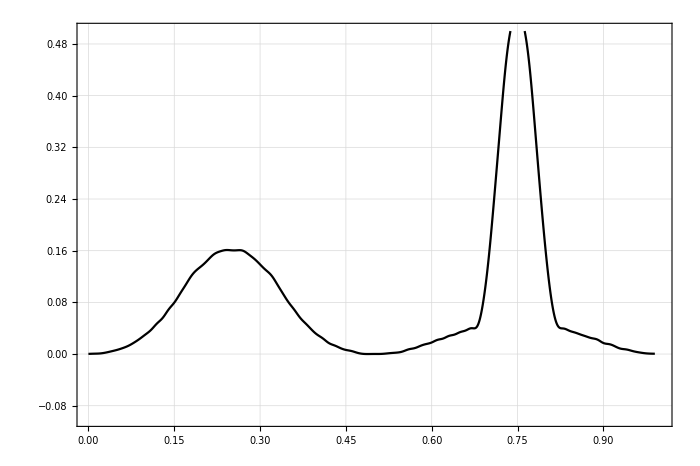

```mathematica
graph=ListPlot[curvedtmp, Joined->True,InterpolationOrder->4,FrameStyle->12, PlotTheme->"Detailed",PlotStyle->RGBColor[0,0,0],FrameStyle->Directive[Black,Thickness[Medium]], AspectRatio->1/1.5,ImageSize->700,PlotRange->{{0,1},{-0.1,0.5}}]
(*Animate[Show[graph,Graphics[Disk[{ii,Interpolation[curved][ii]},0.01],ImageSize->400]],{ii,0,1,1/30}]*)
```

```mathematica
Export["/Users/AShepelev/Documents/Light_curve/disk.gif",Table[plotblyr[1000*Sin[i]+xc, 1000*Cos[i], 200],{i, 0, 2Pi,Pi/30}]]
```

/Users/AShepelev/Documents/Light_curve/disk.gif

```mathematica
N[(T2/T1)^4*Length@PixelValuePositions[plotblyr[1000*Sin[i+ϵ]+xc, 1000*Cos[0], 200],Blue,0.1]+(T3/T1)^4*Length@PixelValuePositions[plotblyr[1000*Sin[i+ϵ]+xc, 1000*Cos[0],200],Yellow,0.1]+Length@PixelValuePositions[plotblyr[1000*Sin[i+ϵ]+xc, 1000*Cos[0],200],Red,0.1]]
```

5276.83

0.991667

```mathematica
curved=Table[{N[curved[[i,1]]],N[curved[[i,2]]]/1.0503745728676666},{i,1,60}]
```

{{0.,1.},{0.0166667,0.998931},{0.0333333,0.99526},{0.05,0.990489},{0.0666667,0.983003},{0.0833333,0.974498},{0.1,0.966199},{0.116667,0.957991},{0.133333,0.95007},{0.15,0.94406},{0.166667,0.934725},{0.183333,0.914063},{0.2,0.89809},{0.216667,0.893052},{0.233333,0.887993},{0.25,0.884692},{0.266667,0.888188},{0.283333,0.893118},{0.3,0.898233},{0.316667,0.914567},{0.333333,0.934834},{0.35,0.943912},{0.366667,0.950429},{0.383333,0.957746},{0.4,0.966347},{0.416667,0.974355},{0.433333,0.982963},{0.45,0.990872},{0.466667,0.995429},{0.483333,0.998522},{0.5,1.00051},{0.516667,0.99849},{0.533333,0.994467},{0.55,0.988936},{0.566667,0.980418},{0.583333,0.970382},{0.6,0.960694},{0.616667,0.94935},{0.633333,0.939045},{0.65,0.928229},{0.666667,0.894233},{0.683333,0.74465},{0.7,0.637555},{0.716667,0.626629},{0.733333,0.616316},{0.75,0.60779},{0.766667,0.615988},{0.783333,0.626323},{0.8,0.636995},{0.816667,0.745518},{0.833333,0.893821},{0.85,0.928194},{0.866667,0.938662},{0.883333,0.949389},{0.9,0.960573},{0.916667,0.970658},{0.933333,0.980036},{0.95,0.988999},{0.966667,0.994353},{0.983333,0.998072}}

```mathematica
Export["/Users/AShepelev/Documents/Light_curve/disk/disk_curve_i000.gif",Table[Show[graph,Graphics[{PointSize->0.02,Point[{{ii,Interpolation[curved][ii]}}]},ImageSize->500]]/.ii->i,{i,0, 1, 1/60}]]
```

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

/Users/AShepelev/Documents/Light_curve/disk/disk_curve_i000.gif

```mathematica
plotlir[ax_,by_,cz_]=Evaluate[Show[ContourPlot3D[{M1/(((x1-x)^2+(y1-y)^2+(z1-z)^2)^0.5)+M2/(((x2-x)^2+(y2-y)^2+(z2-z)^2)^0.5)+(M1+M2)/(x2-x1)^3*√((xc-x)^2+(yc-y)^2)==3.28}, {x, -12, -7.5}, {y, -size, size},{z, -size,size}, ImageSize->800,PlotPoints->20, Mesh->None, ViewPoint->{1000,0,0}, Boxed->False,ContourStyle->Directive[Red],Axes->False,PlotRange->{{-size-3, size-3},{-size,size},{-size,size}},SphericalRegion->True,ViewCenter->{(size-3.5)/size,0.5,0.5},Lighting->{{"Ambient", White}}],Graphics3D[{Blue,Sphere[{x2,y2,z2},R2]},Axes->True],Lighting->{{"Ambient", White}}]]/.{1000,0,0}->{ax,by,cz};
```

```mathematica
Export["/Users/AShepelev/Documents/Light_curve/blyr/blyr_i140.gif",Table[ImageCrop[Rasterize[plotlir[1000*Sin[i],1000*Cos[i],140]],{600,200}],{i,0,2Pi,Pi/30}]]
xc
```

/Users/AShepelev/Documents/Light_curve/blyr/blyr_i140.gif

0

```mathematica
"/Users/AShepelev/Documents/Light_curve/blyr/blyr_i070.gif"
```

0

```mathematica
ImageCrop[Rasterize[plotlir[1000+xc,000,140]],{600,200}]
```

-Graphics-

```mathematica
curvlir= Table[{i/(2Pi),1/17946*((T2/T1)^4*Length@PixelValuePositions[plotlir[1000*Sin[i]+xc, 1000*Cos[i],140],Blue,0.1]+Length@PixelValuePositions[plotlir[1000*Sin[i]+xc, 1000*Cos[i],140],Red,0.1])}, {i, 0, 2Pi, Pi/30}];
```

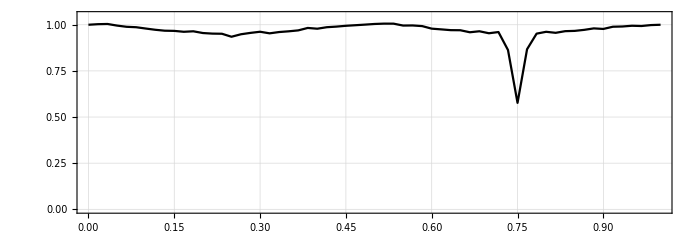

```mathematica
graphlir=ListPlot[curvlir,Joined->True,InterpolationOrder->1,FrameStyle->12, PlotTheme->"Detailed",PlotStyle->RGBColor[0,0,0],FrameStyle->Directive[Black,Thickness[Medium]], AspectRatio->1/3,ImageSize->700,PlotRange->{{0,1},{0,1.05}}]
```

```mathematica
curvlir=N@Table[{curvlir[[i,1]],curvlir[[i,2]]/(117743944/6561)},{i,1, 60}]
```

```mathematica
N[117743944/6561]
```

17946.

```mathematica
Export["/Users/AShepelev/Documents/Light_curve/blyr/blyr_curve_i140.gif",Table[Show[graphlir,Graphics[{PointSize->0.02,Point[{{ii,Interpolation[curvlir][ii]}}]},ImageSize->600]]/.ii->i,{i,0, 1, 1/60}]]
```

/Users/AShepelev/Documents/Light_curve/blyr/blyr_curve_i140.gif